```mathematica
sel={FileNameSetter[Dynamic[f]],Dynamic[f]}
```

{,}

```mathematica
sel[[2]]
```

```mathematica
Import[,"Table"]
```

$Failed

```mathematica
test=Import["/Users/phil/Projetos/NeoPZ_cmake/Projects/Conductivity/Release/condutividade.txt","Table"];
```

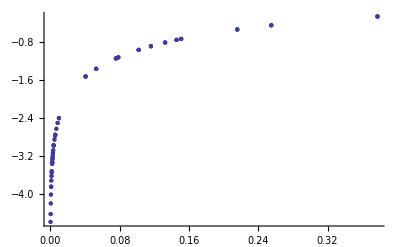

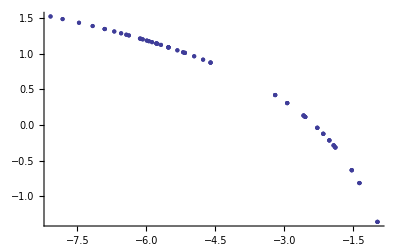

```mathematica
testitem=Transpose[test];
Delta=Transpose[{testitem[[3]],testitem[[-1]]}];
DeltaLog=Transpose[{Log[testitem[[3]]],Log[-testitem[[-1]]]}];
ListPlot[Delta]
g1=ListPlot[DeltaLog]
```

```mathematica
a=Fit[DeltaLog,{1,x,x^2,x^3,x^4},x]
```

-3.03993-2.20875 x-0.514181 x^2-0.0597177 x^3-0.00263789 x^4

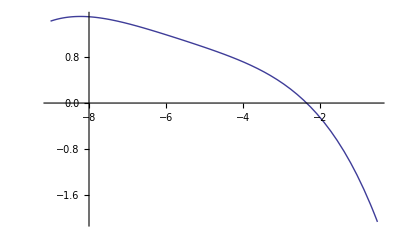

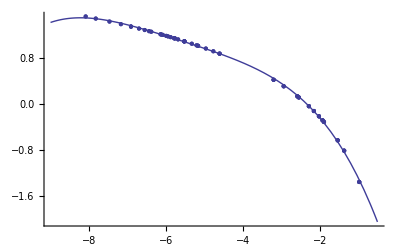

```mathematica
g2=Plot[a,{x,-9,-0.5}]
Show[g1,g2]
```